## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"./a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"./LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"./LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

(*activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];*)
activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];
tmp=Transpose[{activeLEC[[All,1]],activeLEC[[All,3]]/(activeLEC[[All,1]] 200)^3}];
```

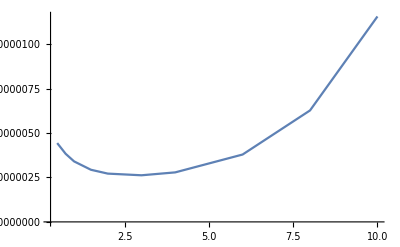

```mathematica
ListPlot[tmp,PlotRange->Full,Joined->True]
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for Dimer-Dimer (AB-AB)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormDD[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (Pi/(4 (2 (core[[i]][[2]]+core[[j]][[2]]+core[[k]][[2]]+core[[l]][[2]]))))^3,{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocDD[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta,w},
eta=(Cc/2.) (π/(2. (Aa+Bb) (Aa+Bb+lam)))^(3./2.);
w=(Aa+Bb) lam/(Aa+Bb+lam);
eta Exp[-w r^2]
];

WnolocDD[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,a1,b1,c1,a2,b2,c2},
zeta1=(π/(2 (Aa+Bb)))^(3./2.) (1./TwoMyOverHBsq);
a1=Bb;
b1=0.;
c1=Aa;

zeta2=-1./2. Cc (π/(Aa+Bb+lam))^(3./2.);

a2=(Aa (Bb+lam)+Bb (Bb+2 lam))/(Aa+Bb+lam);
b2=0.;
c2=Aa;

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∑_j^2 (r^-)_j^2)

```mathematica
NormDD[{{Subscript[c, 1],Subscript[α, 1]},{Subscript[c, 2],Subscript[α, 2]}}]
```

1./(√((π^3 c_1^4)/(32768 α_1^3)+(π^3 c_2^4)/(32768 α_2^3)+(π^3 c_1^3 c_2)/(128 (3 α_1+α_2)^3)+(3 π^3 c_1^2 c_2^2)/(256 (2 α_1+2 α_2)^3)+(π^3 c_1 c_2^3)/(128 (α_1+3 α_2)^3)))

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormDD[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cijkl=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]] a00[[ll]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocDD[i hDif,lam,c0,d0,a00[[ii]][[2]]+a00[[jj]][[2]],a00[[kk]][[2]]+a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocDD[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]]+a00[[jj]][[2]],a00[[kk]][[2]]+a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cijkl (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];



Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2  μ) = ",hbar^2/(2 μ)," MeV·fm^2 =^? ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00207355 MeV     ℏ^2/(2  μ) = 20.7355 MeV·fm^2 =^? 20.7355

```mathematica
GetP2lp1CotD[x_,l_,Energies_]:=Module[{localcore=x,locall=l,ErangeMeV=Energies},

core=localcore;

tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];

AppendTo[tanDs,{Sqrt[mh2 energ],Sqrt[mh2 energ]/Chop[TanDelSwave]}];

(*TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDp,{Sqrt[mh2 energ],Sqrt[mh2 energ]^3/Chop[TanDelPwave]}];*)
,{energ,ErangeMeV}];

kCotDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*k3CotDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]];*) (*Sort all the momentum since it is parallel*)

{kCotDs(*,k3CotDp*)}
]
```

## Import density and fit wavefunctions

```mathematica
wflambdas={6.0};
wfCores=Cases[Import["/home/johannesk/kette_repo/limit_cycles/systems/2/dimer_"<>ToString[NumberForm[#,{12,1}]]<>"_dat","Table"][[2;;]],{_?NumberQ,___}]&/@wflambdas
```

{{{-1.9286,13.964},{-1.2591,4.5822},{-0.90995,0.99901},{-0.31683,0.10874}}}

## The real pudding

```mathematica
RefPfm=Subdivide[0.001,0.25,4];
rGrid={23.4};(*Subdivide[22.5,32.1,2]*)
rr=rGrid[[1]];
EREs={};
lRange=Range[Length[wflambdas]];

nGrid=50;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.02;
k0FMax=0.25;
Divisions=6;
rmip=0.0;
rmap=22;
(*---------------------*)
(*ErangeMeV=Subdivide[k0FMin^2/mh2,k0FMax^2/mh2,Divisions];*)(*N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];*)
ErangeMeV=RefPfm^2/(2 mh2);
Erange1onfm=Sqrt[mh2 ErangeMeV];
exportdataL={};
exportdataS={};
exportdataP={};
```

```mathematica
ll=8;
mycore=wfCores[[1]](* {{1,1}}*)
C0=activeLEC⟦ll⟧⟦2⟧
D0=activeLEC⟦ll⟧⟦3⟧
kCotDs=GetP2lp1CotD[mycore,0.25 activeLEC⟦ll⟧⟦1⟧^2,ErangeMeV]
```

{{-1.9286,13.964},{-1.2591,4.5822},{-0.90995,0.99901},{-0.31683,0.10874}}

-1090.55

6552.5

{{{0.000707107,-0.288522},{0.0447245,-0.286308},{0.0887419,-0.279853},{0.132759,-0.269008},{0.176777,-0.253479}}}

{{-0.288505,1.08911,1.01223},-0.288505+1.08911 p^2+1.01223 p^4}

a = 3.4661              r_1 = 2.1782   v_1 = 1.0122

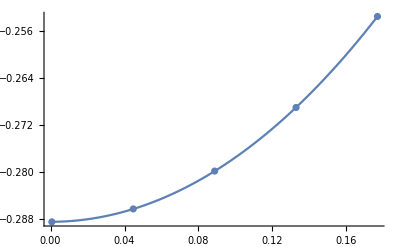

```mathematica
fitData=kCotDs[[1]];
{ereParaS,Tfitp}=Fit[fitData⟦1;;Min[10,Length[fitData[[All,1]]]]⟧,{1,p^2,p^4},p,{"BestFitParameters","BestFit"}]
Print["a = ",NumberForm[-1./ereParaS[[1]],nf],"              r_1 = ",NumberForm[2 ereParaS[[2]],nf],"   v_1 = ",NumberForm[ereParaS[[3]],nf]]
Show[ListPlot[fitData],Plot[Tfitp,{p,fitData[[All,1]][[1]],fitData[[All,1]][[-1]]}]]
```